```mathematica
foilex={{0,-5},{9,2},{18,8},{29,14.5},{39.5,20},{50,25},{60,29},{72,32},{79,33},{85,32.25},{88,31.5},{90,30.80},{94,29},{97.75,26.75},{100,25},{101,23},{102,20},{102,16},{101.75,12.8},{100.5,10},{98,7},{94,5},{91,4},{84.5,3},{77,2.3},{67.5,3},{57,3},{42.5,2},{32,1},{19.5,-1},{10,-2.8},{0,-5}};
```

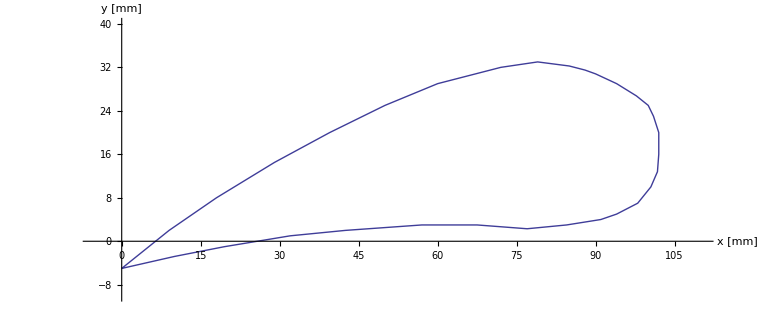

```mathematica
foil=ListPlot[foilex,Joined->True,PlotRange->{{-5,110},{-10,40}},AspectRatio->Automatic,InterpolationOrder->1,PlotStyle->{Thick},AxesLabel->{"x [mm]","y [mm]"}]
```

```mathematica
prespoints={{0,-5},{18,8},{39.5,20},{60,29},{79,33},{90,31},{100,25},{102,16},{100,10},{91,4},{85,3},{67.5,3},{42.5,2},{19.5,-1},{0,-5}};
upppts={{18,8},{39.5,20},{60,29},{79,33},{90,31},{100,25},{102,16}};
lowppts={{102,16},{100,10},{91,4},{85,3},{67.5,3},{42.5,2},{19.5,-1}};
```

```mathematica
ppts=ListPlot[{upppts,lowppts},AspectRatio->Automatic,PlotStyle->{{PointSize[Large],Darker[Green]},{PointSize[Large],Red}}];
Show[foil,ppts]
```